Autor: Radosław Terelak

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 5

Interpolacja Lagrange’a

Napisać procedurę realizującą algorytm interpolacji Lagrange’a (argumenty:  xw, yw). Działanie procedury przetestować na przykładzie z wykładu.

a) Wyznaczyć wielomian interpolacyjny przechodzący przez punkty (1,1), (2,0), (3,2), (4,3), (5,1). Wykonać ilustrację graficzną zadania.

b) Zilustrować zjawisko Rungego interpolując funkcję f(x)=|x| dla x∈ [-1,1]. Podzielić przedział na n równych części (n=2,5,10,14) i jako węzły interpolacji wybrać końce podprzedziałów. Zilustrować otrzymane wyniki.

## Rozwiązanie

### Program

```mathematica
lagrange[xa_,ya_]:=Module[{w=0,n=Length[xa]},
For[i=1,i<=n,i++,
f=1;
For[k=1,k<=i-1,k++,
f=f*(x-xa[[k]])/(xa[[i]]-xa[[k]]);
];
For[k=i+1,k<=n,k++,
f=f*(x-xa[[k]])/(xa[[i]]-xa[[k]]);
];
w=w+ya[[i]]*f;
];
w = Simplify[w];
Print["Wielomian: ",w];
Print[Show[Plot[w,{x,xa[[1]],xa[[n]]}],ListPlot[Thread[{xa,ya}]]]];
Return[w];

]
```

### Przykład testowy

Wielomian: (-1+x)^2

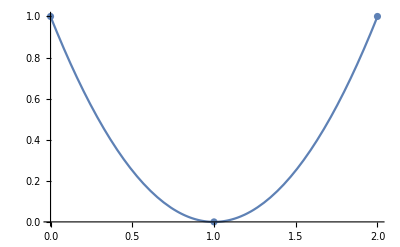

```mathematica
x1= {0,1,2};
y1={1,0,1};
lagrange[x1,y1];
```

### Zadanie a)

Wielomian: 1/12 (132-204 x+101 x^2-18 x^3+x^4)

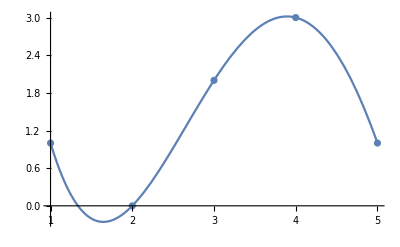

```mathematica
x1={1,2,3,4,5};
y1 = {1,0,2,3,1};
lagrange[x1,y1];
```

### Zadanie b)

n = 2

Wielomian: x^2

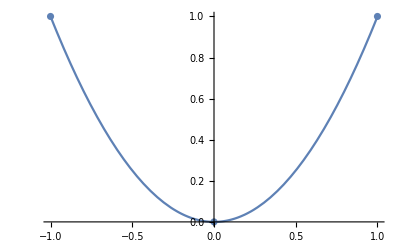

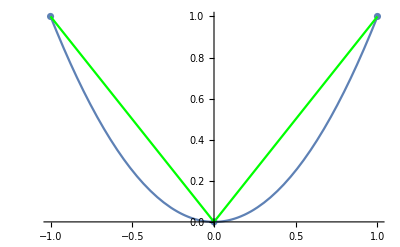

n = 5

Wielomian: 1/192 (27+290 x^2-125 x^4)

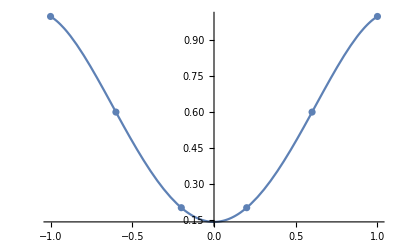

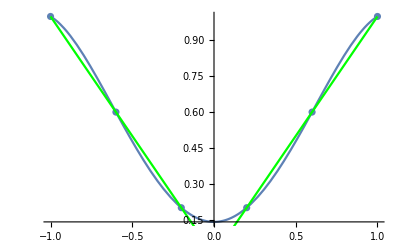

n = 10

Wielomian: (x^2 (234288-1498000 x^2+4659375 x^4-6093750 x^6+2734375 x^8))/36288

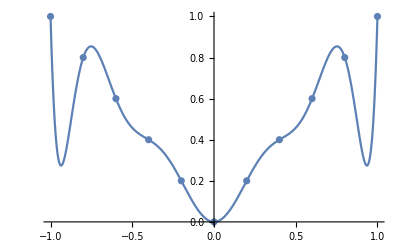

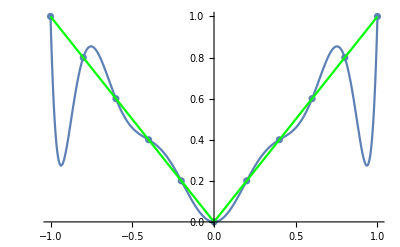

n = 14

Wielomian: (x^2 (683628480-9377776408 x^2+69040097126 x^4-254493728489 x^6+478956961483 x^8-436989210203 x^10+152254159211 x^12))/74131200

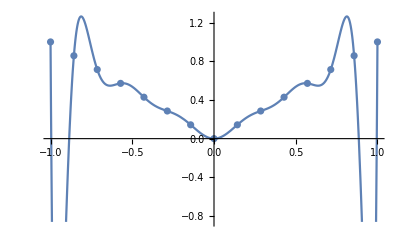

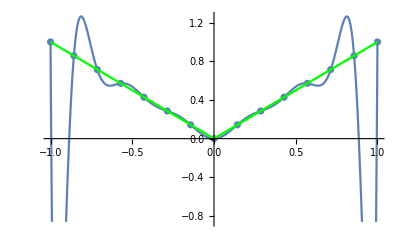

```mathematica
n={2,5,10,14};
For[ix=1,ix≤Length[n],ix++,
x2=Table[i,{i,-1,1,2/n[[ix]]}];
y2=Abs[x2];
Print["n = ",n[[ix]]];
l = lagrange[x2,y2];
Print[Show[Plot[l,{x,-1,1}],ListPlot[Thread[{x2,y2}]],Plot[Abs[x],{x,-1,1},PlotStyle->Green]]];
];
```